## 1.

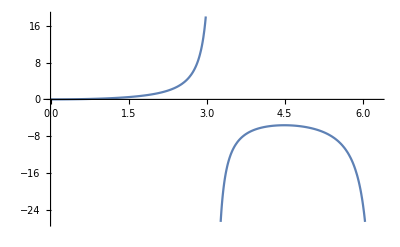

```mathematica
Plot[Abs[Sin[θ]-θ]/Sin[θ],{θ,0,2π}]
```

```mathematica
NSolve[Sin[θ]-θ/Sin[θ]==0.1,θ]
```

NSolve[-θ Csc[θ]+Sin[θ]==0.1,θ]

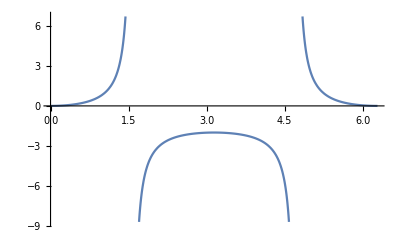

```mathematica
Plot[Abs[Cos[θ]-1]/Cos[θ],{θ,0,2π}]
```

```mathematica
NSolve[Abs[Sin[θ]-θ]/Sin[θ]==0.1,θ]
```

NSolve[Abs[-θ+Sin[θ]] Csc[θ]==0.1,θ]

```mathematica
Degree0.45]
```

°[0.45]

## PI Control System

```mathematica
combined=(-(Kp s+Ki)14/400)/((l s^2-g)(s+14))
```

(7 (-Ki-Kp s))/(200 (14+s) (-g+l s^2))

```mathematica
combined/(1+combined)
```

(7 (-Ki-Kp s))/(200 (14+s) (-g+l s^2) (1+(7 (-Ki-Kp s))/(200 (14+s) (-g+l s^2))))

```mathematica
Simplify[%]
```

(7 (Ki+Kp s))/(7 Ki+200 g (14+s)+s (7 Kp-200 l s (14+s)))

```mathematica
roots=Solve[Denominator[%]==0,s];
```

```mathematica
nroots=s/.roots/.{g->9.8,l->0.04};
```

```mathematica
Manipulate[
ListPlot[
Transpose@{
Re[nroots/.{Ki->mKi,Kp->mKp}],
Im[nroots/.{Ki->mKi,Kp->mKp}]
},
AxesLabel->{"Real","Imaginary"},
PlotRange->{{-50,50},{-100,100}}
],
{{mKi, -48600},-60000,0},
{{mKp, -1600},-60000,0}
]
```

Transpose::nmtx: The first two levels of {Re[nroots],Im[nroots]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[nroots],Im[nroots]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[nroots],Im[nroots]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[nroots],Im[nroots]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[nroots],Im[nroots]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[nroots],Im[nroots]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::nonopt: Options expected (instead of {Im[-(10.4993 (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√Plus[«2»]+0.007056 Kp)^(1/3)+6.61417 (3.60013+0.001512 Ki+√Plus[«2»]+0.007056 Kp)^(1/3)],Im[((5.24967+9.0927 ⅈ)«1»(«1»«1»)/(«1»)^(1/3)-(3.30709-«18» ⅈ) («1»)^(«1»)],Im[((5.24967-9.0927 ⅈ) (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√Plus[«1»]+0.007056 Kp)^(1/3)-(3.30709+5.72804 ⅈ) (3.60013+«2»+0.007056 Kp)^(1/3)]}) beyond position 1 in ListPlot[{-14/3+Re[-(10.4993 (-1.4896+Times[«2»]))/Plus[«4»]^(1/3)+6.61417 Plus[«4»]^(1/3)],-14/3+Re[((5.24967+9.0927 ⅈ) (-1.4896+Times[«2»]))/Plus[«4»]^(1/3)-(3.30709-5.72804 ⅈ) Plus[«4»]^(1/3)],-14/3+Re[((5.24967-9.0927 ⅈ) (-1.4896+Times[«2»]))/Plus[«4»]^(1/3)-(3.30709+5.72804 ⅈ) Plus[«4»]^(1/3)]},{Im[-(10.4993 (-1.4896+0.0042 Kp))/(3.60013+«1»+«1»+Times[«2»])^(1/3)+6.61417 (3.60013+«3»)^(1/3)],«1»,Im[((«1») («1»))/(«1»)-(«19»+«1») «1»]}]. An option must be a rule or a list of rules.

ListPlot[{-14/3+Re[-((10.4993 (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3))+6.61417 (3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)],-14/3+Re[((5.24967+9.0927 ⅈ) (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)-(3.30709-5.72804 ⅈ) (3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)],-14/3+Re[((5.24967-9.0927 ⅈ) (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)-(3.30709+5.72804 ⅈ) (3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)]},{Im[-((10.4993 (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3))+6.61417 (3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)],Im[((5.24967+9.0927 ⅈ) (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)-(3.30709-5.72804 ⅈ) (3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)],Im[((5.24967-9.0927 ⅈ) (-1.4896+0.0042 Kp))/(3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)-(3.30709+5.72804 ⅈ) (3.60013+0.001512 Ki+√(4 (-1.4896+0.0042 Kp)^3+(3.60013+0.001512 Ki+0.007056 Kp)^2)+0.007056 Kp)^(1/3)]}]

```mathematica
Apart[combined/(1+combined)]
```

(7 (Ki+Kp s))/(-2800 g+7 Ki-200 g s+7 Kp s+2800 l s^2+200 l s^3)

## Motor + Angle Feedback

```mathematica
motor = (b*a)/(s + a); 
errmotor = jp + ji/s; 
feedmotor = Factor[1/(1/(motor + errmotor))]
```

(a ji+a b s+ji s+a jp s+jp s^2)/(s (a+s))

```mathematica
errangle=kp+ki/s;
v2angle=s/(l s^2-g);
plant=Factor[feedmotor v2angle]
```

(a ji+a b s+ji s+a jp s+jp s^2)/((a+s) (-g+l s^2))

```mathematica
total=Simplify[(errangle plant)/(1+errangle plant)]
```

((ki+kp s) (s (ji+jp s)+a (ji+(b+jp) s)))/(a ji (ki+kp s)+ji s (ki+kp s)+a s (-g+jp ki+jp kp s+l s^2+b (ki+kp s))+s^2 (-g+l s^2+jp (ki+kp s)))

```mathematica
roots1=Solve[Denominator[%]==0, s];
```

```mathematica
nroots1=s/.roots1/.{a-> 14, b-> 1/400, g-> 9.8, l-> 0.04};
```

```mathematica
Manipulate[
ListPlot[
Transpose@{
Re[nroots1/.{ki->mKi,kp->mKp, ji-> mji, jp-> mjp}],
Im[nroots1/.{ki->mKi,kp->mKp, ji-> mji, jp-> mjp}]
},
AxesLabel->{"Real","Imaginary"},
PlotRange->All
],
{{mKi, 400},-10000,2000},
{{mKp, 1030},-4000, 3000}, 
{{mji, 3350}, -1000, 6000},
{{mjp, 1710}, 0, 4000}
]
```

## Position Controller

```mathematica
controllerPlant=kp+ki/s;
motorPlant = (b*a)/(s + a);
pendulumPlant=s/(l s^2-g);
```

```mathematica
errorFunction=θd[s]/(1-k/s controllerPlant*motorPlant-controllerPlant*motorPlant*pendulumPlant)
```

θd[s]/(1-(a b k (kp+ki/s))/(s (a+s))-(a b (kp+ki/s) s)/((a+s) (-g+l s^2)))

```mathematica
vals={
a->14,
b->1/400,
g->9.8,
l->.04
};
```

```mathematica
transferFunction=(errorFunction*controllerPlant*motorPlant*pendulumPlant)/θd[s](*/.vals*)
```

(a b (kp+ki/s) s)/((a+s) (-g+l s^2) (1-(a b k (kp+ki/s))/(s (a+s))-(a b (kp+ki/s) s)/((a+s) (-g+l s^2))))

```mathematica
Simplify[transferFunction]
```

-(a b s^2 (ki+kp s))/(a s^2 (g-l s^2)+s^3 (g-l s^2)+a b (ki+kp s) (-g k+(1+k l) s^2))

```mathematica
denom=Denominator[Simplify[transferFunction]]
```

a s^2 (g-l s^2)+s^3 (g-l s^2)+a b (ki+kp s) (-g k+(1+k l) s^2)

```mathematica
(denom/.{ki->400,kp->1030, k-> 3350}/.vals)==0
```

14 s^2 (9.8-0.04 s^2)+s^3 (9.8-0.04 s^2)+7/200 (400+1030 s) (-32830.+135. s^2)==0

```mathematica
Solve[%]
```

{{s→-355.693},{s→-15.5944},{s→-0.388333},{s→15.5942},{s→342.081}}

```mathematica
Manipulate[
ListPlot[
Transpose@{
Re[s/.Solve[(denom/.{ki->mKi,kp->mKp, k-> mk}/.vals)==0,s]],
Im[s/.Solve[(denom/.{ki->mKi,kp->mKp, k-> mk}/.vals)==0,s]]
},
AxesLabel->{"Real","Imaginary"},
PlotRange->All
],
{{mKi, -7280},-10000,-4000},
{{mKp, -580},-2000, 1000}, 
{{mk, -0.5}, -50, 50}
]
```